```mathematica
SetDirectory["/home/s1220054/Dissertation/Dissertation/DiSamp/src"]
```

/home/s1220054/Dissertation/Dissertation/DiSamp/src

```mathematica
typelist=Table[Import["type_"<>ToString[i]<>".txt","CSV"],{i,20}]
```

{{{0,0},{193,431},{193,432},{193,433},{193,434},{194,430},{194,431},{195,430},{195,431},{195,432},{196,430},{196,431},{196,432},{196,433},{196,434},{196,435},{197,430},{197,431},{197,432},{197,433},{197,434},{197,435},{198,430},{198,431},{198,432},{198,433},{198,434},{198,435},{198,453},{198,454},{199,428},{199,429},{199,430},{199,431},{199,432},{199,433},{199,434},{199,435},{199,453},{199,454},{200,428},{200,429},{200,430},{200,431},{200,432},{200,433},{200,434},{200,435},{200,436},{200,453},{200,454},{200,459},{201,425},{201,426},{201,427},{201,428},{201,429},{201,430},{201,431},{201,432},{201,433},{201,434},24494,{510,317},{510,318},{510,319},{510,321},{510,322},{510,323},{510,324},{510,325},{511,303},{511,304},{511,305},{511,306},{511,307},{511,308},{511,309},{511,310},{511,311},{511,312},{511,313},{511,314},{511,315},{511,316},{511,318},{511,323},{511,324},{512,304},{512,305},{512,306},{512,307},{512,308},{512,309},{512,310},{512,312},{512,313},{512,314},{512,323},{513,305},{513,306},{513,307},{513,308},{513,309},{513,310},{513,314},{513,315},{513,316},{514,305},{514,306},{514,307},{514,308},{514,309},{514,310},{514,314},{515,305},{515,306},{515,307},{515,308},{515,309},{515,310},{516,308},{516,309},{517,308},{517,309}},18,{1}}
 |  |  |  |

```mathematica
typelist[[1]]
```

{{0,0},{193,431},{193,432},{193,433},{193,434},{194,430},{194,431},{195,430},{195,431},{195,432},{196,430},{196,431},{196,432},{196,433},{196,434},{196,435},{197,430},{197,431},{197,432},{197,433},{197,434},{197,435},{198,430},{198,431},{198,432},{198,433},{198,434},{198,435},{198,453},{198,454},{199,428},{199,429},{199,430},{199,431},{199,432},{199,433},{199,434},{199,435},{199,453},{199,454},{200,428},{200,429},{200,430},{200,431},{200,432},{200,433},{200,434},{200,435},{200,436},{200,453},{200,454},{200,459},{201,425},{201,426},{201,427},{201,428},{201,429},{201,430},{201,431},{201,432},{201,433},{201,434},{201,435},24492,{510,316},{510,317},{510,318},{510,319},{510,321},{510,322},{510,323},{510,324},{510,325},{511,303},{511,304},{511,305},{511,306},{511,307},{511,308},{511,309},{511,310},{511,311},{511,312},{511,313},{511,314},{511,315},{511,316},{511,318},{511,323},{511,324},{512,304},{512,305},{512,306},{512,307},{512,308},{512,309},{512,310},{512,312},{512,313},{512,314},{512,323},{513,305},{513,306},{513,307},{513,308},{513,309},{513,310},{513,314},{513,315},{513,316},{514,305},{514,306},{514,307},{514,308},{514,309},{514,310},{514,314},{515,305},{515,306},{515,307},{515,308},{515,309},{515,310},{516,308},{516,309},{517,308},{517,309}}
 |  |  |  |

```mathematica
typelist[[2]]
```

{{0,0},{335,346},{335,347},{336,344},{336,345},{336,346},{337,344},{337,345},{337,346},{338,345},{338,346},{339,345}}

```mathematica
typelist[[3]]
```

{{0,0},{325,446},{326,438},{326,439},{326,440},{326,441},{326,442},{326,443},{326,444},{326,445},{326,446},{326,447},{326,448},{326,449},{327,437},{327,438},{327,439},{327,440},{327,441},{327,442},{327,443},{327,444},{327,445},{327,446},{327,447},{327,448},{328,436},{328,437},{328,438},{328,439},{328,440},{328,441},{328,442},{328,443},{328,444},{328,445},{328,446},{328,447},{328,448},{328,449},{329,437},{329,438},{329,439},{329,440},{329,441},{329,442},{329,443},{329,444},{329,445},{329,446},{329,447},{329,448},{330,436},{330,437},{330,438},{330,439},{330,440},{330,441},{330,442},{330,443},{330,444},{330,445},{330,446},{330,447},3955,{403,504},{403,505},{403,506},{403,507},{403,508},{403,509},{403,510},{403,511},{404,496},{404,497},{404,498},{404,499},{404,500},{404,501},{404,502},{404,503},{404,504},{404,505},{404,506},{404,507},{404,508},{404,509},{404,510},{405,497},{405,498},{405,499},{405,500},{405,501},{405,502},{405,503},{405,504},{405,505},{405,506},{405,507},{405,508},{405,509},{405,510},{406,499},{406,500},{406,501},{406,502},{406,503},{406,504},{406,505},{406,506},{406,507},{406,508},{406,509},{406,510},{407,499},{407,500},{407,501},{407,502},{407,503},{407,504},{407,505},{407,506},{407,507},{407,508},{407,509},{408,502},{408,504},{408,505}}
 |  |  |  |

```mathematica
typelist[[9]]
```

{{0,0},{328,351},{329,350},{329,351},{330,350},{330,351},{331,351}}

```mathematica
typelist[[12]]
```

{{0,0},{327,366},{328,365},{328,366},{328,367},{329,366},{329,367},{330,366},{330,367}}

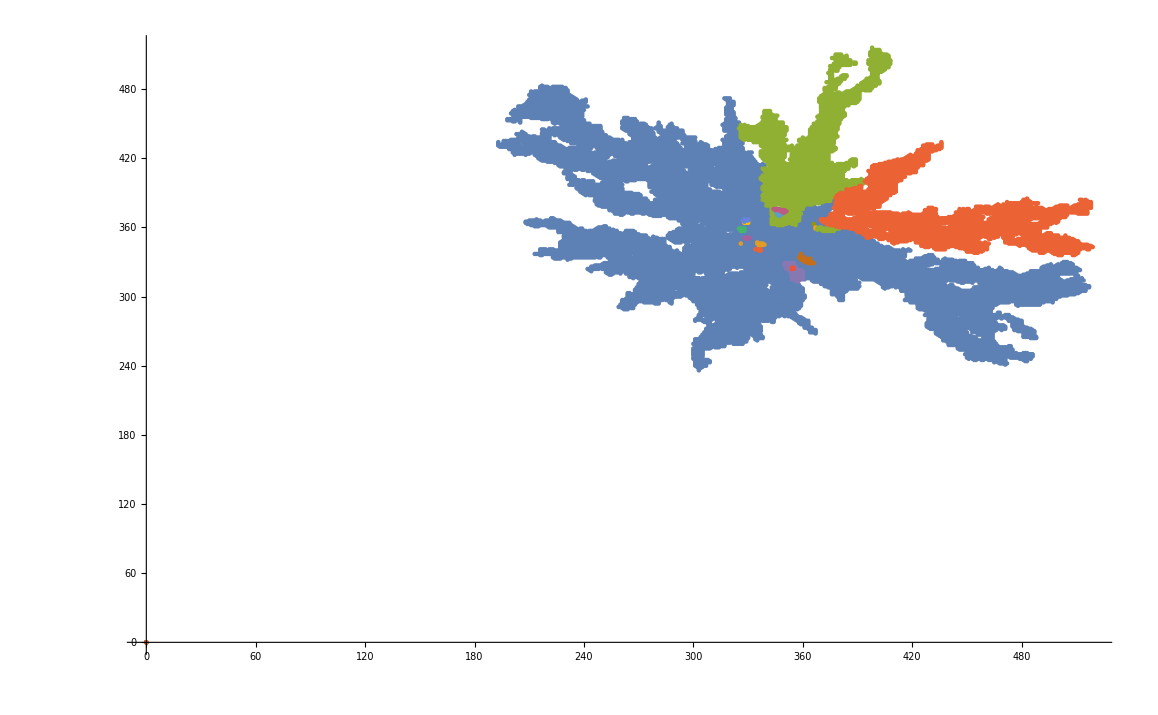

Part::partw: Part 3 of {0, 0} does not exist.

```mathematica
ListPlot[{typelist[[1]],typelist[[2]],typelist[[3]],typelist[[4]],typelist[[5]],typelist[[6]],typelist[[7]],typelist[[8]],typelist[[9]],typelist[[10]],typelist[[11]], typelist[[12]], typelist[[13]], typelist[[14]], typelist[[15]], typelist[[16]], typelist[[17]], typelist[[18]], typelist[[19]]}]
```

```mathematica
data =Import["xi.txt", "CSV"]
```

{{0,11},{1,0},{2,0},{3,0},{4,0},{5,0},{6,0},{7,0},{8,0},{9,0},{10,0}}

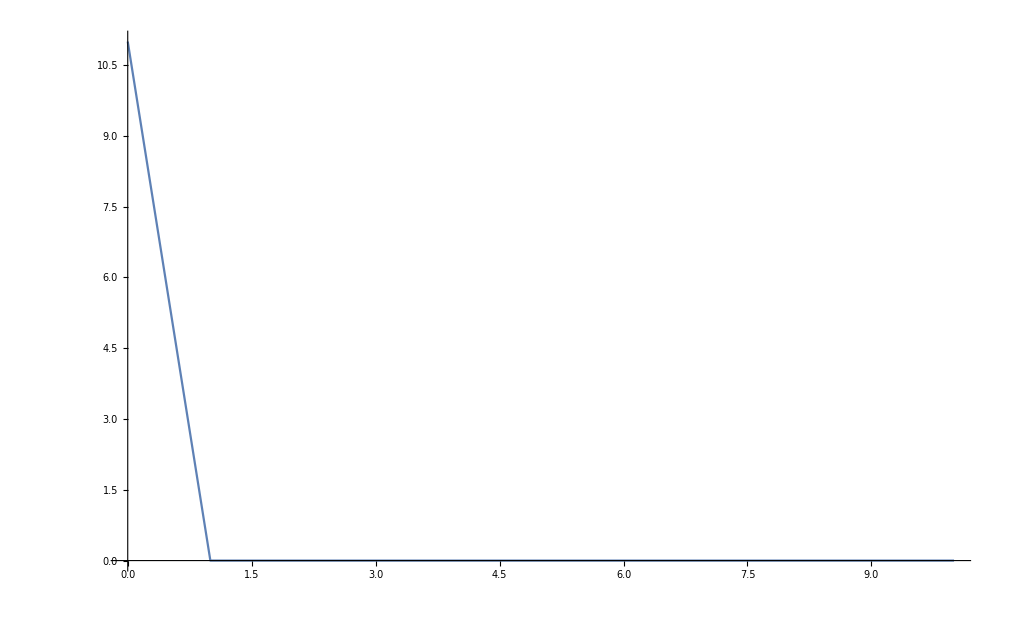

```mathematica
ListLinePlot[data]
```

```mathematica
datanew=Import["array.txt", "CSV"]
```

{1}
 |  |  |  |

```mathematica
ArrayPlot[datanew]
```

-Graphics-